```mathematica
ClearAll["Global`*"];
```

```mathematica
NotebookDirectory[];

(* Your folder structure should be as follows: 
simulation_dimension_sweep/initializations/each_cell_dimension_set/simulation_output_files  *)
(*I recommend splitting your x- and y-dimension sweeps into different simulation_dimesnion_sweep folders for ease of importing*)

(*list the initialization folders for each simulation*)
fileList={
"init_1",
"init_2",
"init_3",
"init_4"
};
```

```mathematica
(* for simulations pulling in the x-direction *)
makestresstrainx[folder_]:= {
(*PULLING AND COLLATING DATA FROM THE SIMULATIONS*)
(*imports data from the simulation outputs*)
inStretch = {};
inEnergy = {};
For[i = 1, i≤Length@fileList,i++,
AppendTo[inStretch, Import[#,"CSV"]&/@FileNames["StretchOut.dat",NotebookDirectory[]<>folder<>fileList⟦i⟧,Infinity]];
AppendTo[inEnergy, Import[#]&/@FileNames["EnergyOut.dat",NotebookDirectory[]<> folder<>fileList⟦i⟧,Infinity]];
];

(*isolates relevant data from the files; only grabs total energy*)
stretchTab = inStretch⟦;;,;;,1,2;;3⟧;
totEnergy = inEnergy[[;;,;;,3]];

(*puts all the data together into one list*)
energyTab = Table[Table[{stretchTab[[i,j,1]], stretchTab[[i,j,2]], i, totEnergy[[i, j, 1]]},{j, 1, Length@totEnergy[[i]]}], {i, 1, Length@totEnergy}];
energyTabGathered = GatherBy[Flatten[energyTab,1], First] ;

(*sorts the table by energy for each a_x*)
energyTabSorted = Table[SortBy[energyTabGathered[[i]], Last],{i, 1, Length@energyTabGathered}];

(*gets rid of runs with unphysical results*)
(*should check your starting dimension and initialization if you get lots of unphysical results*)
energyTabSorted = Table[DeleteMissing[Table[If[0.001< energyTabSorted[[i,j, 2]]<30 && 0.01< energyTabSorted[[i,j, 4]]<5,{energyTabSorted[[i,j,1]],energyTabSorted[[i,j,2]],energyTabSorted[[i,j,3]], energyTabSorted[[i,j, 4]]},Missing[]],{j, 1, Length@energyTabSorted[[i]]}]],{i,1,Length@energyTabSorted}];
energyTabCleaned = {};
For[i=1,i≤Length@energyTabSorted, i++,If[Length@energyTabSorted[[i]]!=0,AppendTo[energyTabCleaned, energyTabSorted[[i]]] ]];

(*isolates the minimum energy run for each a_x*)
minEnergy = SortBy[energyTabCleaned[[;;,1]],First];
(*min energy is xdim ydim init energy*)



(* FIND THE ZERO FORCE CELL DIMENSIONS *)
(*energy v a_x*)
roughinterpolate = Table[{minEnergy[[i,1]], minEnergy[[i, 4]]},{i, 1, Length@minEnergy}];

(*small interpolation near zeroforce for more accuracy in calculating xmin*)
(* to find the minimum, you need a guess of where the minimum is. See documentation for FindMinimum.*)
smallinterpolate= DeleteMissing[Table[If[roughinterpolate[[i, 2]]<1,{roughinterpolate[[i,1]], roughinterpolate[[i, 2]]},Missing[]],{i, 1, Length@roughinterpolate}]];
mininterpolate = Interpolation[smallinterpolate, InterpolationOrder->3];
minimum = FindMinimum[mininterpolate[x],{x, 2.8}];
minx = x/.minimum[[2]];

(*find miny with linear fit, use interpolation to calculate the strain in y*)
dims = Table[{minEnergy[[i, 1]], minEnergy[[i,2]]}, {i, 1, Length@minEnergy}];
yfit = Fit[dims, {1, x}, x];
miny = yfit/.{x->minx};


(*find discrete derivative to caclculate the force*)
force = {};
For[i=2,i<Length@minEnergy,i++, AppendTo[force, (minEnergy[[i+1,4]]-minEnergy[[i-1,4]])/(minEnergy[[i+1,1]]-minEnergy[[i-1,1]])]];

(*divide force by miny to get stress*)
stressx = Table[force[[i]]/miny,{i,1,Length@force}];

(*linear strain in x*)
strainx = Table[(minEnergy[[i,1]]-minx)/minx,{i,2,Length@minEnergy}];

(*linear strain in y*)
strainy = Table[(minEnergy[[i,2]]-miny)/miny, {i,2,Length@minEnergy}];


(* fordatx give all stress and strain data for each direction, used to export data *)
stressy=0;
fordatx = Table[{stressx[[i]], stressy, strainx[[i]],strainy[[i]]},{i,1,Length@stressx}];

(*returns strain in x and stress in x*)
stressstrain = Table[{strainx[[i]],stressx[[i]]},{i,1,Length@stressx}]
}



(* for simulations pulling in the y-direction *)
makestresstrainy[folder_]:= {
(*imports data from the simulation outputs*)
inStretch = {};
inEnergy = {};
For[i = 1, i≤Length@fileList,i++,
AppendTo[inStretch, Import[#,"CSV"]&/@FileNames["StretchOut.dat",NotebookDirectory[]<>folder<>fileList⟦i⟧,Infinity]];
AppendTo[inEnergy, Import[#]&/@FileNames["EnergyOut.dat",NotebookDirectory[]<> folder<>fileList⟦i⟧,Infinity]];
];

(*isolates relevant data from the files*)
stretchTab = inStretch⟦;;,;;,1,2;;3⟧;
totEnergy = inEnergy[[;;,;;,3]];

(*HERE IS THE DIFFERENCE BETWEEN X,Y !!!!!!!!!!!!!!!!!!!*)
(*RIGHT HERE*)
(*puts all the data together into one list*)
(*instead of x,y,initfile,energy like above, its y,x,initfile,energy*)
energyTab = Table[Table[{stretchTab[[i,j,2]], stretchTab[[i,j,1]], i, totEnergy[[i, j, 1]]},{j, 1, Length@totEnergy[[i]]}], {i, 1, Length@totEnergy}];
energyTabGathered = GatherBy[Flatten[energyTab,1], First] ;

(*sorts the table by energy for each a_y*)
energyTabSorted = Table[SortBy[energyTabGathered[[i]], Last],{i, 1, Length@energyTabGathered}];
energyTabSorted = Table[DeleteMissing[Table[If[0.001< energyTabSorted[[i,j, 2]]<30 && 0.01< energyTabSorted[[i,j, 4]]<5,{energyTabSorted[[i,j,1]],energyTabSorted[[i,j,2]],energyTabSorted[[i,j,3]], energyTabSorted[[i,j, 4]]},Missing[]],{j, 1, Length@energyTabSorted[[i]]}]],{i,1,Length@energyTabSorted}];
energyTabCleaned = {};
For[i=1,i≤Length@energyTabSorted, i++,If[Length@energyTabSorted[[i]]!=0,AppendTo[energyTabCleaned, energyTabSorted[[i]]] ]];

(*isolates the minimum energy run for each a_y*)
minEnergy = SortBy[energyTabCleaned[[;;,1]],First];
minEnergy = DeleteMissing[Table[If[0.01< minEnergy[[i, 2]]<30 && 0.01< minEnergy[[i, 4]]<30,{minEnergy[[i,1]],minEnergy[[i,2]],minEnergy[[i,3]], minEnergy[[i, 4]]},Missing[]],{i, 1, Length@minEnergy}]];
(*min energy is ydim xdim init energy*)

(* FIND THE ZERO FORCE CELL DIMENSIONS *)
(*energy v a_y*)
roughinterpolate = Table[{minEnergy[[i,1]], minEnergy[[i, 4]]},{i, 1, Length@minEnergy}];

(*small interpolation near zeroforce for more accuracy in calculating xmin*)
(* to find the minimum, you need a guess of where the minimum is. See documentation for FindMinimum.*)
smallinterpolate= DeleteMissing[Table[If[roughinterpolate[[i, 2]]<1,{roughinterpolate[[i,1]], roughinterpolate[[i, 2]]},Missing[]],{i, 1, Length@roughinterpolate}]];
mininterpolate = Interpolation[smallinterpolate, InterpolationOrder->3];
minimum = FindMinimum[mininterpolate[x],{x, 2.1}];
miny = x/.minimum[[2]];

(*find minx using a linear fit to cell idmension data*)
dims = Table[{minEnergy[[i, 1]], minEnergy[[i,2]]}, {i, 1, Length@minEnergy}];
fitx = Fit[dims, {1, x}, x];
minx = fitx/.{x->miny};

(*find discrete derivative to caclculate the force*)
force = {};
For[i=2,i<Length@minEnergy,i++, AppendTo[force, (minEnergy[[i+1,4]]-minEnergy[[i-1,4]])/(minEnergy[[i+1,1]]-minEnergy[[i-1,1]])]];

(* take force and divide by zero-froce x-dimension for stress*)
stressy = Table[force[[i]]/minx,{i,1,Length@force}];

(* linear strain in y *)
strainy = Table[(minEnergy[[i,1]]-miny)/miny,{i,2,Length@minEnergy}];

(*linear strain in x *)
strainx = Table[(minEnergy[[i,2]]-minx)/minx, {i,2,Length@minEnergy}];

(* fordatx give all stress and strain data for each direction, used to export data *)
stressx=0;
fordaty = Table[{stressx,stressy[[i]],strainx[[i]], strainy[[i]]},{i,1,Length@stressy}];

(* ouputs strain in y, stress in yy*)
stressstrain = Table[{strainy[[i]],stressy[[i]]},{i,1,Length@stressy}]
}


(* joins x and y stretching data into one output file *)
makedatfile[datx_,daty_ ]:= {
dat=Join[datx,daty];
SetDirectory[NotebookDirectory[]];
Export["stockinetteacrylic.dat", dat, "CSV"]
}
```

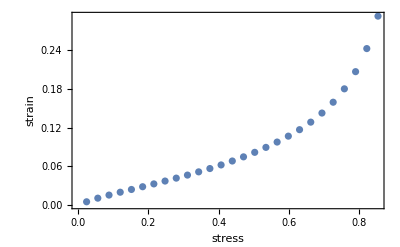

```mathematica
x300= makestresstrainx["core300x/"];
x300= x300[[1]];
ListPlot[x300, Frame->True, FrameLabel->{"stress", "strain"}]
makedatx = fordatx;
```

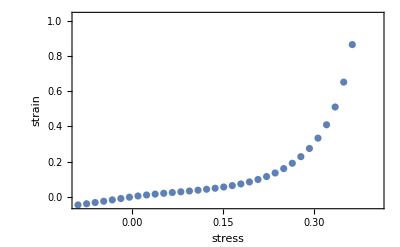

2.11949

```mathematica
y300 = makestresstrainy["core300y/"];
y300=y300[[1]];
ListPlot[y300, Frame->True, FrameLabel->{"stress", "strain"}]
makedaty = fordaty;
miny
```

```mathematica
makedatfile[fordatx,fordaty]
```

{stockinetteacrylic.dat}